# Collimated Flux Investigation (RMS + FWHM)

## Units + Constants

```mathematica
(*Units*)
MeV=10^6;
keV=10^3;
nC=10^-9;
pC=10^-12;
μJ=10^-6;
nm=10^-9;
mrad=10^-3;
mm=10^-3;
cm=10^-2;
μm=10^-6;
MHz=10^6;
ps=10^-12;
bn=10^-28;
```

```mathematica
(*Constants*)
σT=6.65245871548*10^-29;
re=2.8179403262*10^-15;
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
me=0.51099895MeV; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*Angles*)
fivedeg=(5*π)/180;
```

## Plotting

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## Cases

The optimised values within these cases are using the Compton_Optimisation_Parrallel.nb code, which is outdated (doesn’t include hourglass effect), but is the best for comparing to spectra etc.

```mathematica
CBETA150base={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->1cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.5mrad};
CBETA150optRMS={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->12.6189cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.43333mrad};
CBETA150optFWHM={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->26.9211cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.256mrad};

DIANA687base={Ee->687MeV,ϕ->fivedeg,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->0.2,ϵn->0.5mm mrad,σL->25 μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.1mrad};
DIANA687optRMS={Ee->687MeV,ϕ->fivedeg,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->0.603575,ϵn->0.5mm mrad,σL->25 μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.09181mrad};
DIANA687optFWHM={Ee->687MeV,ϕ->fivedeg,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->1.6067,ϵn->0.5mm mrad,σL->25 μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.055mrad};


DIANA1519optRMS={Ee->1519MeV,ϕ->fivedeg,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->1.600,ϵn->0.5mm mrad,σL->25μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.04269mrad};
```

## Integrated Cross Section Calculation

## Intermediaries

```mathematica
(*Scattered photon energy equations*) 
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/λ; (*in eV, using hbar*)
```

## Scattered Photon Energy

```mathematica
Eγ[Ee_,ϕ_,λ_,θ_]:=(EL[λ]*(1+β[Ee]*Cos[ϕ]))/(1-β[Ee]*Cos[θ]+EL[λ]/Ee*(1+Cos[ϕ+θ]));
```

```mathematica
Eγ[Ee,ϕ,λ,0]/.CBETA150optRMS
```

402516.

## Lorentz Invariants (from Mandelstam Variables)

```mathematica
X[Ee_,ϕ_,λ_]:=(2*γ[Ee]*EL[λ]*(1+β[Ee]*Cos[ϕ]))/me;
Y[Ee_,ϕ_,λ_,θ_]:=(2*γ[Ee]*Eγ[Ee,ϕ,λ,θ]*(1-β[Ee]*Cos[θ]))/me;
```

## Y Angular Variation

```mathematica
XYvsθCBETA=Table[{θ/mrad,X[Ee,ϕ,λ]/.CBETA150optRMS,Y[Ee,0,λ,θ]/.CBETA150optRMS},{θ,0,1/γ[Ee]/.CBETA150optRMS,1/(100*γ[Ee])/.CBETA150optRMS}];
```

```mathematica
XYvsθDIANA=Table[{θ/mrad,X[Ee,ϕ,λ]/.DIANA687optRMS,Y[Ee,0,λ,θ]/.DIANA687optRMS},{θ,0,1/γ[Ee]/.DIANA687optRMS,1/(100*γ[Ee])/.DIANA687optRMS}];
```

```mathematica
CBETAXYvsθ=ListLinePlot[{Partition[Riffle[XYvsθCBETA⟦All,1⟧,XYvsθCBETA⟦All,2⟧],2],Partition[Riffle[XYvsθCBETA⟦All,1⟧,XYvsθCBETA⟦All,3⟧],2]},Frame->True,FrameLabel->{"Collimation Angle [mrad]","X/Y" },LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",PlotLegends->Placed[LineLegend[{"X","Y"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.3}],ImageSize->Medium];
```

```mathematica
DIANAXYvsθ=ListLinePlot[{Partition[Riffle[XYvsθDIANA⟦All,1⟧,XYvsθDIANA⟦All,2⟧],2],Partition[Riffle[XYvsθDIANA⟦All,1⟧,XYvsθDIANA⟦All,3⟧],2]},Frame->True,FrameLabel->{"Collimation Angle [mrad]","X/Y" },LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",PlotLegends->Placed[LineLegend[{"X","Y"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.3}],ImageSize->Medium];
```

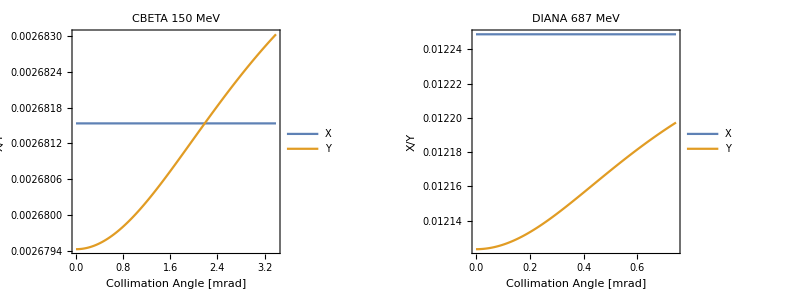

```mathematica
Grid[{{CBETAXYvsθ,DIANAXYvsθ}}]
```

## Cross Section [Berestetskii, σ = f(Y)]

```mathematica
dσdY[Ee_,ϕ_,λ_,θ_]:=(8*π*re^2)/X[Ee,ϕ,λ]^2*((1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ])^2+1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ]+1/4*(X[Ee,ϕ,λ]/Y[Ee,ϕ,λ,θ]+Y[Ee,ϕ,λ,θ]/X[Ee,ϕ,λ]));
```

## Lorentz Invariant Y Differential [Me, Y = f(θ)]

```mathematica
dYdθ[Ee_,θ_,ϕ_,λ_]:=(X[Ee,ϕ,λ]*β[Ee]*Sin[θ]*(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)-X[Ee,ϕ,λ]*(1-β[Ee]*Cos[θ])*(β[Ee]*Sin[θ]-EL[λ]/Ee*Sin[ϕ+θ]))/(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)^2;
```

## Cross Section [Me, σ = f(θ)]

```mathematica
dσdθ[Ee_,ϕ_,λ_,θ_]:=dσdY[Ee,ϕ,λ,θ]*dYdθ[Ee,θ,ϕ,λ];
```

```mathematica
Off[NIntegrate::nlim,NIntegrate::inumr];
```

```mathematica
σ[Ee_,ϕ_,λ_,θcol_]:=NIntegrate[dσdθ[Ee,ϕ,λ,θ],{θ,0,θcol}];
```

## Cross Section Investigation

```mathematica
Grid[{{"CBETA Cross Sections [bn]",SpanFromLeft,SpanFromLeft},{"Baseline","RMS Optimization","FWHM Optimization"},{(σ[Ee,ϕ,λ,θcol]/.CBETA150base)/bn,(σ[Ee,ϕ,λ,θcol]/.CBETA150optRMS)/bn,(σ[Ee,ϕ,λ,θcol]/.CBETA150optFWHM)/bn}},Dividers->All]
```

CBETA Cross Sections [bn] |  | 
Baseline | RMS Optimization | FWHM Optimization
0.0208606 | 0.0158358 | 0.00564784

```mathematica
CBETAσvsθ=Table[{θ/mrad,σ[Ee,ϕ,λ,θ]/σT/.CBETA150optRMS,σ[Ee,ϕ,λ,θ]/σT/.CBETA150base},{θ,-1/γ[Ee]/.CBETA150base,1/γ[Ee]/.CBETA150base,1/(200*γ[Ee])/.CBETA150base}];
```

```mathematica
DIANAσvsθ=Table[{θ/mrad,σ[Ee,ϕ,λ,θ]/σT/.DIANA687optRMS,σ[Ee,ϕ,λ,θ]/σT/.DIANA687base},{θ,-1/γ[Ee]/.DIANA687base,1/γ[Ee]/.DIANA687base,1/(200*γ[Ee])/.DIANA687base}];
```

```mathematica
baseCBETAσvsθ=ListLinePlot[Partition[Riffle[CBETAσvsθ⟦All,1⟧,CBETAσvsθ⟦All,2⟧],2],Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline CBETA 150 MeV",FrameLabel->{"Collimation Angle [mrad]","Int. Cross Section [σ/σ_T]"},ImageSize->Medium];
```

```mathematica
baseDIANAσvsθ=ListLinePlot[Partition[Riffle[DIANAσvsθ⟦All,1⟧,DIANAσvsθ⟦All,2⟧],2],Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline DIANA 687 MeV",FrameLabel->{"Collimation Angle [mrad]","Int. Cross Section [σ/σ_T]"},ImageSize->Medium];
```

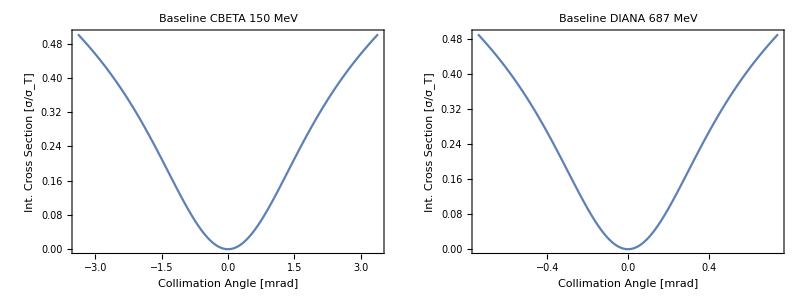

```mathematica
Grid[{{baseCBETAσvsθ,baseDIANAσvsθ}}]
```

## Integrated Cross Section Investigation

## Integrated Cross Section Plots

```mathematica
σvsθCBETA150=Table[{θ/mrad,(σ[Ee,0,λ,θ]/.CBETA150optRMS)/σT,(σ[Ee,ϕ,λ,θ]/.CBETA150optRMS)/σT,(σ[Ee,(45*π)/180,λ,θ]/.CBETA150optRMS)/σT,(σ[Ee,(90*π)/180,λ,θ]/.CBETA150optRMS)/σT,(σ[Ee,(270*π)/180,λ,θ]/.CBETA150optRMS)/σT},{θ,-1/γ[Ee]/.CBETA150optRMS,1/γ[Ee]/.CBETA150optRMS,1/(100*γ[Ee])/.CBETA150optRMS}];
```

```mathematica
σvsθDIANA687=Table[{θ/mrad,(σ[Ee,0,λ,θ]/.DIANA687optRMS)/σT,(σ[Ee,ϕ,λ,θ]/.DIANA687optRMS)/σT,(σ[Ee,(45*π)/180,λ,θ]/.DIANA687optRMS)/σT,(σ[Ee,(90*π)/180,λ,θ]/.DIANA687optRMS)/σT,(σ[Ee,(270*π)/180,λ,θ]/.DIANA687optRMS)/σT},{θ,-1/γ[Ee]/.DIANA687optRMS,1/γ[Ee]/.DIANA687optRMS,1/(100*γ[Ee])/.DIANA687optRMS}];
```

```mathematica
σvsθDIANA1519=Table[{θ/mrad,(σ[Ee,0,λ,θ]/.DIANA1519optRMS)/σT,(σ[Ee,ϕ,λ,θ]/.DIANA1519optRMS)/σT,(σ[Ee,(45*π)/180,λ,θ]/.DIANA1519optRMS)/σT,(σ[Ee,(90*π)/180,λ,θ]/.DIANA1519optRMS)/σT,(σ[Ee,(270*π)/180,λ,θ]/.DIANA1519optRMS)/σT},{θ,-1/γ[Ee]/.DIANA1519optRMS,1/γ[Ee]/.DIANA1519optRMS,1/(100*γ[Ee])/.DIANA1519optRMS}];
```

```mathematica
csCBETA150=ListLinePlot[{Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,2⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,3⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,4⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,5⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,6⟧],2]},Frame->True,PlotStyle->{Red,Blue,Orange,Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",FrameLabel->{"Collimation Angle [mrad]","Norm. Int. Cross Section [σ/σ_T]"},PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 5°","ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.6}],ImageSize->Medium];
```

```mathematica
csDIANA687=ListLinePlot[{Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,2⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,3⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,4⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,5⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,6⟧],2]},Frame->True,PlotStyle->{Red,Blue,Orange,Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",FrameLabel->{"Collimation Angle [mrad]","Norm. Int. Cross Section [σ/σ_T]"},PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 5°","ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.6}],ImageSize->Medium];
```

```mathematica
csDIANA1519=ListLinePlot[{Partition[Riffle[σvsθDIANA1519⟦All,1⟧,σvsθDIANA1519⟦All,2⟧],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,σvsθDIANA1519⟦All,3⟧],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,σvsθDIANA1519⟦All,4⟧],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,σvsθDIANA1519⟦All,5⟧],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,σvsθDIANA1519⟦All,6⟧],2]},Frame->True,PlotStyle->{Red,Blue,Orange,Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 1519 MeV",FrameLabel->{"Collimation Angle [mrad]","Norm. Int. Cross Section [σ/σ_T]"},PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 5°","ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.6}],ImageSize->Medium];
```

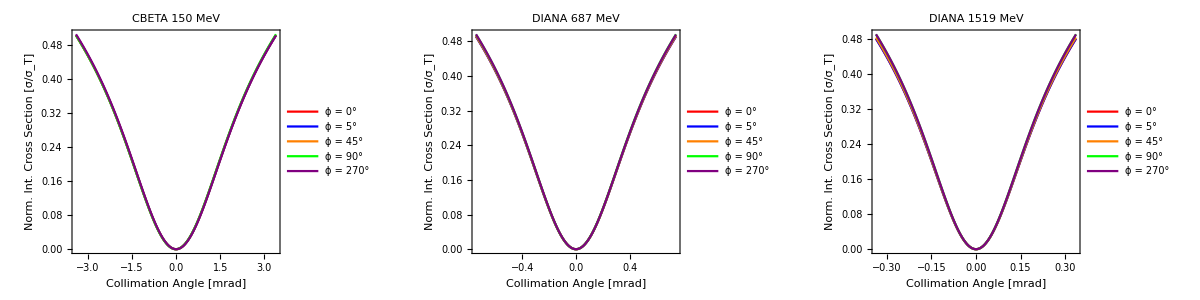

```mathematica
Grid[{{csCBETA150,csDIANA687,csDIANA1519}}]
```

## Integrated Cross Section Residuals

```mathematica
REScsCBETA150=ListLinePlot[{Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,4⟧)*10^3],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,5⟧)*10^3],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,6⟧)*10^3],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",FrameLabel->{"Collimation Angle [mrad]","Residual [(σ (0  °) - σ (ϕ))/σ_T ×10^-3]"},PlotLegends->Placed[LineLegend[{"ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.18,0.45}],ImageSize->Medium];
```

```mathematica
REScsDIANA687=ListLinePlot[{Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,4⟧)*10^3],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,5⟧)*10^3],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,6⟧)*10^3],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",FrameLabel->{"Collimation Angle [mrad]","Residual [(σ (0  °) - σ (ϕ))/σ_T×10^-3]"},PlotLegends->Placed[LineLegend[{"ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.3}],ImageSize->Medium];
```

```mathematica
REScsDIANA1519=ListLinePlot[{Partition[Riffle[σvsθDIANA1519⟦All,1⟧,(σvsθDIANA1519⟦All,2⟧-σvsθDIANA1519⟦All,4⟧)*10^2],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,(σvsθDIANA1519⟦All,2⟧-σvsθDIANA1519⟦All,5⟧)*10^2],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,(σvsθDIANA1519⟦All,2⟧-σvsθDIANA1519⟦All,6⟧)*10^2],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 1519 MeV",FrameLabel->{"Collimation Angle [mrad]","Residual [(σ (0  °) - σ (ϕ))/σ_T×10^-2]"},PlotLegends->Placed[LineLegend[{"ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.5,0.3}],ImageSize->Medium];
```

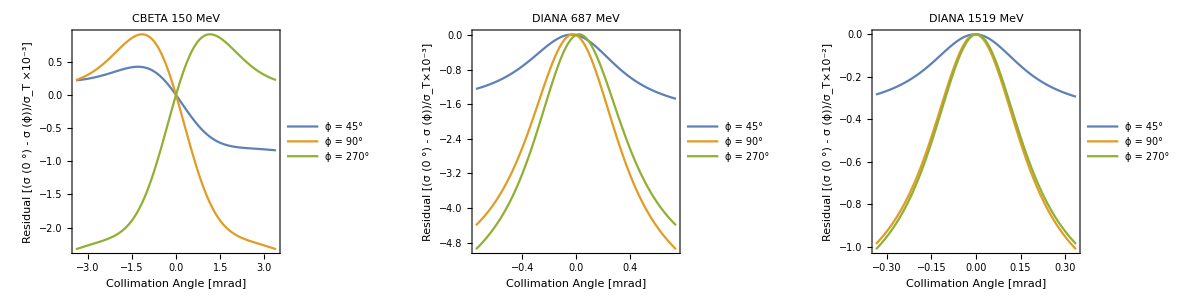

```mathematica
Grid[{{REScsCBETA150,REScsDIANA687,REScsDIANA1519}}]
```

## Collimated Flux Calculation [My Method]

## Collimated Flux Intermediaries

```mathematica
(*Luminosity equations*)
Ne[Q_]:=Q/elecharge;
NL[Epulse_,λ_]:=Epulse/(elecharge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
σzl[tpulse_]:=clight*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
```

## Head-on Luminosity

```mathematica
L[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_]:=(Ne[Q]*NL[Epulse,λ])/(2*π*convxy[βIP,ϵn,Ee,σL]^2);
```

## Angular Crossing Luminosity Reduction Factor

```mathematica
RAC[βIP_,ϵn_,Ee_,σL_,ϕ_,σze_,tpulse_]:=(convxy[βIP,ϵn,Ee,σL]*Cos[ϕ])/Sqrt[convxy[βIP,ϵn,Ee,σL]^2*Cos[ϕ]^2+convz[σze,tpulse]^2*Sin[ϕ]^2];
```

## Collimated Flux [Me]

```mathematica
Fcol[Ee_,ϕ_,λ_,θcol_,βIP_,ϵn_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=σ[Ee,ϕ,λ,θcol]*RAC[βIP,ϵn,Ee,σL,ϕ,σze,tpulse]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

## Collimated Flux [My Method] Investigation

## CBETA Flux Cases

```mathematica
FcolCBETA150base=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base},{θ,0,1/γ[Ee]/.CBETA150base,1/(100*γ[Ee])/.CBETA150base}];
```

```mathematica
FcolCBETA150optRMS=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS},{θ,0,1/γ[Ee]/.CBETA150optRMS,1/(100*γ[Ee])/.CBETA150optRMS}];
```

```mathematica
baseFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,2⟧],2],Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
optFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150optRMS⟦All,1⟧,FcolCBETA150optRMS⟦All,2⟧],2],Partition[Riffle[FcolCBETA150optRMS⟦All,1⟧,FcolCBETA150optRMS⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"0.5% rms BW Optimised CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
zerodegFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,2⟧],2],Partition[Riffle[FcolCBETA150optRMS⟦All,1⟧,FcolCBETA150optRMS⟦All,2⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 0°) CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Baseline","rms Optimised"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],ImageSize->Medium];
```

```mathematica
fivedegFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,3⟧],2],Partition[Riffle[FcolCBETA150optRMS⟦All,1⟧,FcolCBETA150optRMS⟦All,3⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 5°) CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Baseline","rms Optimised"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],ImageSize->Medium];
```

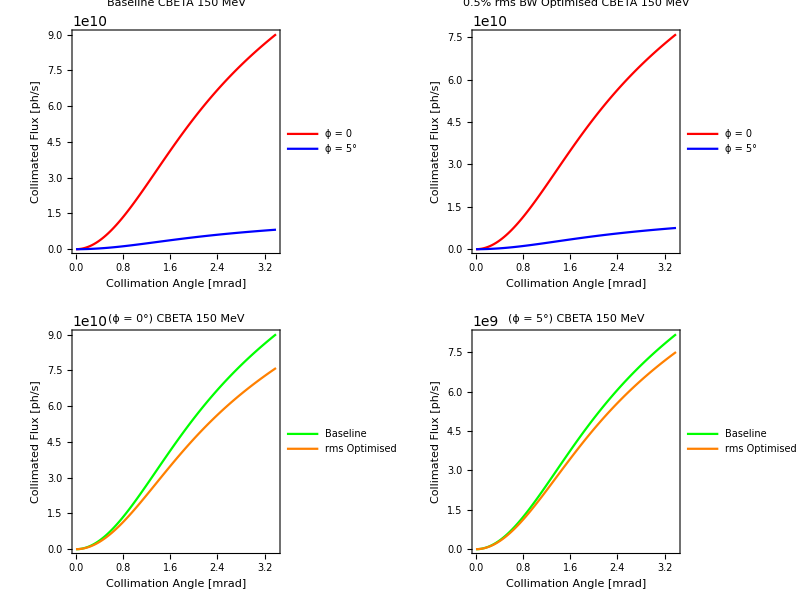

```mathematica
Grid[{{baseFcolCBETA,optFcolCBETA},{zerodegFcolCBETA,fivedegFcolCBETA}}]
```

## DIANA Flux Cases

```mathematica
FcolDIANA687base=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base},{θ,0,1/γ[Ee]/.DIANA687base,1/(100*γ[Ee])/.DIANA687base}];
```

```mathematica
FcolDIANA687optRMS=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS},{θ,0,1/γ[Ee]/.DIANA687optRMS,1/(100*γ[Ee])/.DIANA687optRMS}];
```

```mathematica
baseFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,2⟧],2],Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
optFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687optRMS⟦All,1⟧,FcolDIANA687optRMS⟦All,2⟧],2],Partition[Riffle[FcolDIANA687optRMS⟦All,1⟧,FcolDIANA687optRMS⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"0.5% rms BW Optimised DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
zerodegFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,2⟧],2],Partition[Riffle[FcolDIANA687optRMS⟦All,1⟧,FcolDIANA687optRMS⟦All,2⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 0°) DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Baseline","rms Optimised"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],ImageSize->Medium];
```

```mathematica
fivedegFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,3⟧],2],Partition[Riffle[FcolDIANA687optRMS⟦All,1⟧,FcolDIANA687optRMS⟦All,3⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 5°) CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Baseline","rms Optimised"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.7}],ImageSize->Medium];
```

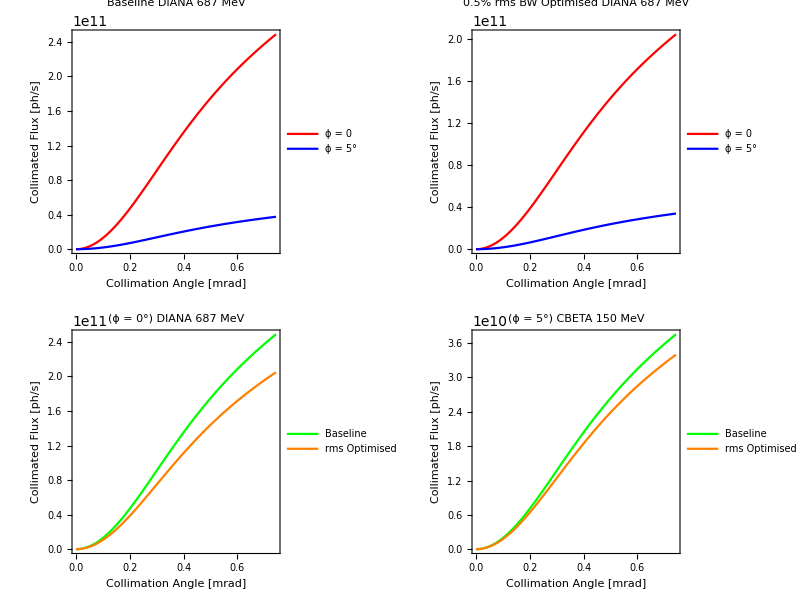

```mathematica
Grid[{{baseFcolDIANA,optFcolDIANA},{zerodegFcolDIANA,fivedegFcolDIANA}}]
```

## Analytical Collimated Flux Comparative Methods

## Collimated Flux Comparative Methods Intermediaries

```mathematica
(*Cross section in the Thomson limit i.e as X->0*)
σc[Ee_,ϕ_,λ_]:=σT*(1-X[Ee,ϕ,λ]);
(*Rayleigh Range*)
zr[σL_,λ_]:=(4*π*σL^2)/λ;
(*Acceptance angle for Collimation Equations*)
ψ[Ee_,θ_]:=γ[Ee]*θ;
```

## F_(0.1%) Method

```mathematica
F01[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_,f_,ϕ_,σze_,tpulse_]:=3/2*10^-3*σc[Ee,ϕ,λ]*RAC[βIP,ϵn,Ee,σL,ϕ,σze,tpulse]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

## Angular Spread Method (3/2 γ^2 θ_col^2×F)

This is a method Geoff used. I’m not sure where it comes from! ASK HIM!

```mathematica
FAS[Ee_,θ_,λ_,βIP_,ϵn_,σL_,ϕ_,σze_,tpulse_,Q_,Epulse_,f_]:=3/2*γ[Ee]^2*θ^2*σc[Ee,ϕ,λ]*RAC[βIP,ϵn,Ee,σL,ϕ,σze,tpulse]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

## Curatolo F_ψ Method

```mathematica
FψCuratolo[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_,f_,θ_,ϕ_,σze_,tpulse_]:=σc[Ee,ϕ,λ]*RAC[βIP,ϵn,Ee,σL,ϕ,σze,tpulse]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f*((1+(CubeRoot[X[Ee,ϕ,λ]]*ψ[Ee,θ]^2)/3)*ψ[Ee,θ]^2)/((1+(1+X[Ee,ϕ,λ]/2)ψ[Ee,θ]^2)*(1+ψ[Ee,θ]^2));
```

## Analytical Collimated Flux Comparative Methods Investigation

```mathematica
FψCBETA=Table[{θ/mrad,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ,ϕ,σze,tpulse]/.CBETA150optRMS,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ,ϕ,σze,tpulse]/.CBETA150base},{θ,0,1/γ[Ee]/.CBETA150base,1/(100*γ[Ee])/.CBETA150base}];
```

```mathematica
FψDIANA=Table[{θ/mrad,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ,ϕ,σze,tpulse]/.DIANA687optRMS,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ,ϕ,σze,tpulse]/.DIANA687base},{θ,0,1/γ[Ee]/.DIANA687base,1/(100*γ[Ee])/.DIANA687base}];
```

```mathematica
FASCBETA=Table[{θ/mrad,FAS[Ee,θ,λ,βIP,ϵn,σL,ϕ,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS,FAS[Ee,θ,λ,βIP,ϵn,σL,ϕ,σze,tpulse,Q,Epulse,f]/.CBETA150base},{θ,0,1/γ[Ee]/.CBETA150base,1/(100*γ[Ee])/.CBETA150base}];
```

```mathematica
FASDIANA=Table[{θ/mrad,FAS[Ee,θ,λ,βIP,ϵn,σL,ϕ,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS,FAS[Ee,θ,λ,βIP,ϵn,σL,ϕ,σze,tpulse,Q,Epulse,f]/.DIANA687base},{θ,0,1/γ[Ee]/.DIANA687base,1/(100*γ[Ee])/.DIANA687base}];
```

```mathematica
baseCBETAFψvsFcol=ListLinePlot[{Partition[Riffle[FψCBETA⟦All,1⟧,FψCBETA⟦All,3⟧],2],Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,3⟧],2],Partition[Riffle[FASCBETA⟦All,1⟧,FASCBETA⟦All,3⟧],2]},PlotStyle->{Green,Purple,Red},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Curatolo","Me","3/2γ^2θ_col^2×F"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
optCBETAFψvsFcol=ListLinePlot[{Partition[Riffle[FψCBETA⟦All,1⟧,FψCBETA⟦All,2⟧],2],Partition[Riffle[FcolCBETA150optRMS⟦All,1⟧,FcolCBETA150optRMS⟦All,3⟧],2],Partition[Riffle[FASCBETA⟦All,1⟧,FASCBETA⟦All,2⟧],2]},PlotStyle->{Green,Purple,Red},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"rms Optimised CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Curatolo","Me","3/2γ^2θ_col^2×F"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
baseDIANAFψvsFcol=ListLinePlot[{Partition[Riffle[FψDIANA⟦All,1⟧,FψDIANA⟦All,3⟧],2],Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,3⟧],2],Partition[Riffle[FASDIANA⟦All,1⟧,FASDIANA⟦All,3⟧],2]},PlotStyle->{Green,Purple,Red},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Curatolo","Me","3/2γ^2θ_col^2×F"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
optDIANAFψvsFcol=ListLinePlot[{Partition[Riffle[FψDIANA⟦All,1⟧,FψDIANA⟦All,2⟧],2],Partition[Riffle[FcolDIANA687optRMS⟦All,1⟧,FcolDIANA687optRMS⟦All,3⟧],2],Partition[Riffle[FASDIANA⟦All,1⟧,FASDIANA⟦All,2⟧],2]},PlotStyle->{Green,Purple,Red},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"rms Optimised DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Curatolo","Me","3/2γ^2θ_col^2×F"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

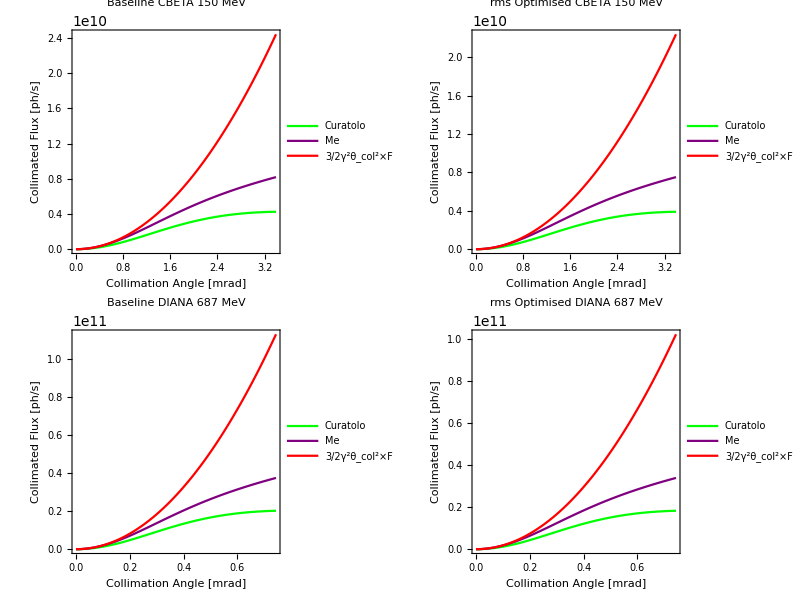

```mathematica
Grid[{{baseCBETAFψvsFcol,optCBETAFψvsFcol},{baseDIANAFψvsFcol,optDIANAFψvsFcol}}]
```

## ICARUS Collimated Flux Calculations

## CBETA 150 MeV

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA"];
CBETA150RMS=<<"CBETA150_RMS_200M.txt";
CBETA150FWHM=<<"CBETA150_FWHM_100M.txt";
CBETA150BASE=<<"CBETA150BASE0.5mrad_20M.txt";
```

Note that the ICARUS data here isn’t exactly optimised for the head-on case , it is for a 5° crossing angle.

```mathematica
CBETAoptRMSICARUSIntFlux=Integrate[Interpolation[CBETA150RMS][x],{x,Min[CBETA150RMS⟦All,1⟧],Max[CBETA150RMS⟦All,1⟧]}]*f*Q/nC/.CBETA150optRMS
```

3.45231×10^9

```mathematica
CBETAoptFWHMICARUSIntFlux=Integrate[Interpolation[CBETA150FWHM][x],{x,Min[CBETA150FWHM⟦All,1⟧],Max[CBETA150FWHM⟦All,1⟧]}]*f*Q/nC/.CBETA150optFWHM
```

1.051×10^9

```mathematica
CBETAbaseICARUSIntFlux=Integrate[Interpolation[CBETA150BASE][x],{x,Min[CBETA150BASE⟦All,1⟧],Max[CBETA150BASE⟦All,1⟧]}]*f*Q/nC/.CBETA150base
```

4.93189×10^9

## DIANA 687 MeV

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/DIANA/7MeV_15MVm"];
DIANA687RMS=<<"DIANA687_RMS_100M.txt";
DIANA687FWHM=<<"DIANA687_FWHM_50M.txt";
DIANA687BASE=<<"DIANA687BASE0.1mrad_20M.txt";
```

```mathematica
DIANAoptRMSICARUSIntFlux=Integrate[Interpolation[DIANA687RMS][x],{x,Min[DIANA687RMS⟦All,1⟧],Max[DIANA687RMS⟦All,1⟧]}]*f*Q/nC/.DIANA687optRMS
```

8.75747×10^9

```mathematica
DIANAoptFWHMICARUSIntFlux=Integrate[Interpolation[DIANA687FWHM][x],{x,Min[DIANA687FWHM⟦All,1⟧],Max[DIANA687FWHM⟦All,1⟧]}]*f*Q/nC/.DIANA687optFWHM
```

2.26909×10^9

```mathematica
DIANAbaseICARUSIntFlux=Integrate[Interpolation[DIANA687BASE][x],{x,Min[DIANA687BASE⟦All,1⟧],Max[DIANA687BASE⟦All,1⟧]}]*f*Q/nC/.DIANA687base
```

1.2219×10^10

## ICCS3D Collimated Flux Calculations

Note that the ICCS3D data here isn’t exactly optimised for the head-on case , it is optimized for a 5° crossing angle.

## CBETA 150 MeV

```mathematica
rawdataCBETA=Import["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA/CBETA150_RMS_ICCS3D_FINAL.txt","Words"];
ndataCBETA=Length[rawdataCBETA];
ncolumnsCBETA=6;
ndatCBETA=ndataCBETA/ncolumnsCBETA;
BalsaICCSCBETA=Array[Ω,{2,ndatCBETA}];
For[i=0,i<(ndatCBETA+1),i++,
(*for energy*)
Ω[1,i]=Interpreter["Number"][ToString[rawdataCBETA⟦1+ncolumnsCBETA*(i-1)⟧]]*1/keV;
(*for specden*)
Ω[2,i]=Interpreter["Number"][ToString[rawdataCBETA⟦3+ncolumnsCBETA*(i-1)⟧]]*(keV*nC)/elecharge;
];
BalsaValsCBETA=Array[Υ,{2,0}];
For[i=1,i<Length[Transpose[BalsaICCSCBETA]]+1,i++,
If[BalsaICCSCBETA⟦2,i⟧>10^-20,
AppendTo[BalsaValsCBETA⟦1⟧,BalsaICCSCBETA⟦1,i⟧];
AppendTo[BalsaValsCBETA⟦2⟧,BalsaICCSCBETA⟦2,i⟧];
];
];
```

```mathematica
BalsaValsCBETA=Transpose[BalsaValsCBETA];
```

```mathematica
CBETAoptRMSICCS3DIntFlux=Integrate[Interpolation[BalsaValsCBETA][x],{x,Min[BalsaValsCBETA⟦All,1⟧],Max[BalsaValsCBETA⟦All,1⟧]}]*f*Q/nC/.CBETA150optRMS
```

3.57972×10^9

## DIANA 687 MeV

Note that the ICCS3D data here is optimised for the head-on case , not for a 5° crossing angle. The factor of 10 is introduced as Balsa needed this in order to correctly + quickly simulate the laser pulse.

```mathematica
rawdataDIANA=Import["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/DIANA/7MeV_15MVm/DIANA687_RMS_ICCS3D.txt","Words"];
ndataDIANA=Length[rawdataDIANA];
ncolumnsDIANA=6;
ndatDIANA=ndataDIANA/ncolumnsDIANA;
BalsaICCSDIANA=Array[η,{2,ndatDIANA}];
For[i=0,i<(ndatDIANA+1),i++,
(*for energy*)
η[1,i]=Interpreter["Number"][ToString[rawdataDIANA⟦1+ncolumnsDIANA*(i-1)⟧]]*1/MeV;
(*for specden*)
η[2,i]=Interpreter["Number"][ToString[rawdataDIANA⟦3+ncolumnsDIANA*(i-1)⟧]]*10*(MeV*nC)/elecharge;
];
BalsaValsDIANA=Array[υ,{2,0}];
For[i=1,i<Length[Transpose[BalsaICCSDIANA]]+1,i++,
If[BalsaICCSDIANA⟦2,i⟧>10^-20,
AppendTo[BalsaValsDIANA⟦1⟧,BalsaICCSDIANA⟦1,i⟧];
AppendTo[BalsaValsDIANA⟦2⟧,BalsaICCSDIANA⟦2,i⟧];
];
];
```

```mathematica
BalsaValsDIANA=Transpose[BalsaValsDIANA];
```

```mathematica
DIANAoptRMSICCS3DIntFlux=Integrate[Interpolation[BalsaValsDIANA][x],{x,Min[BalsaValsDIANA⟦All,1⟧],Max[BalsaValsDIANA⟦All,1⟧]}]*f*Q/nC/.DIANA687optRMS
```

9.08257×10^9

## ICARUS + ICCS3D Plots

## CBETA 150 MeV

```mathematica
CBETAoptRMSPLOT=ListLinePlot[{CBETA150RMS,BalsaValsCBETA},PlotStyle->{Red,Blue},Frame->True,PlotLabel->"CBETA 150 MeV rms 0.5% BW",FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{"ICARUS","ICCS3D"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{388,405},{0,110}},ImageSize->Medium];
CBETAoptFWHMPLOT=ListLinePlot[CBETA150FWHM,PlotStyle->{Red},Frame->True,PlotLabel->"CBETA 150 MeV FWHM 0.5% BW",FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},ImageSize->Medium];
CBETAbasePLOT=ListLinePlot[CBETA150BASE,PlotStyle->{Red},Frame->True,PlotLabel->"CBETA 150 MeV Baseline (θ_col = 0.5 mrad)",FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},ImageSize->Medium];
```

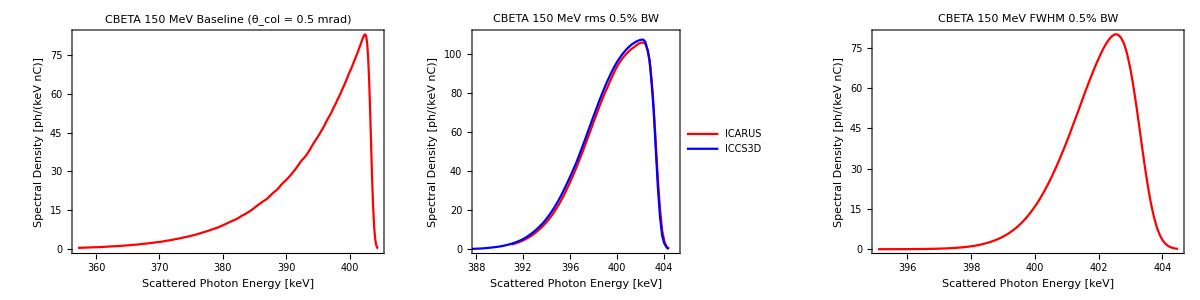

```mathematica
Grid[{{CBETAbasePLOT,CBETAoptRMSPLOT,CBETAoptFWHMPLOT}}]
```

## DIANA 687 MeV

```mathematica
DIANAoptRMSPLOT=ListLinePlot[{DIANA687RMS,BalsaValsDIANA},PlotStyle->{Red,Blue},Frame->True,PlotLabel->"DIANA 687 MeV rms 0.5% BW",FrameLabel->{"Scattered Photon Energy [MeV]","Spectral Density [ph/(MeV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{"ICARUS","ICCS3D"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{8,8.37},{0,7000}},ImageSize->Medium];
DIANAoptFWHMPLOT=ListLinePlot[DIANA687FWHM,PlotStyle->{Red},Frame->True,PlotLabel->"DIANA 687 MeV FWHM 0.5% BW",FrameLabel->{"Scattered Photon Energy [MeV]","Spectral Density [ph/(MeV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotRange->Full,ImageSize->Medium];
DIANAbasePLOT=ListLinePlot[DIANA687BASE,PlotStyle->{Red},Frame->True,PlotLabel->"DIANA 687 MeV Baseline (θ_col = 0.1 mrad)",FrameLabel->{"Scattered Photon Energy [MeV]","Spectral Density [ph/(MeV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotRange->{{7.7,8.4},{0,8000}},ImageSize->Medium];
```

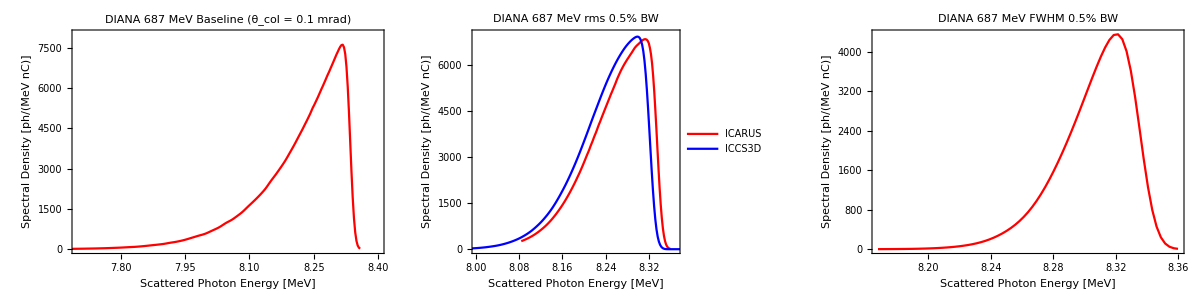

```mathematica
Grid[{{DIANAbasePLOT,DIANAoptRMSPLOT,DIANAoptFWHMPLOT}}]
```

## FWHM and RMS Comparison

```mathematica
CBETAoptRMSFWHMPLOT=ListLinePlot[{CBETA150RMS,CBETA150FWHM},PlotStyle->{Red,Blue},Frame->True,PlotLabel->"CBETA 150 MeV: ICARUS",FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{"rms 0.5% BW","FWHM 0.5% BW"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{390,405},{0,110}},ImageSize->Medium];
```

```mathematica
DIANAoptRMSFWHMPLOT=ListLinePlot[{DIANA687RMS,DIANA687FWHM},PlotStyle->{Red,Blue},Frame->True,PlotLabel->"DIANA 687 MeV: ICARUS",FrameLabel->{"Scattered Photon Energy [MeV]","Spectral Density [ph/(MeV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{"rms 0.5% BW","FWHM 0.5% BW"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{8,8.37},{0,7000}},ImageSize->Medium];
```

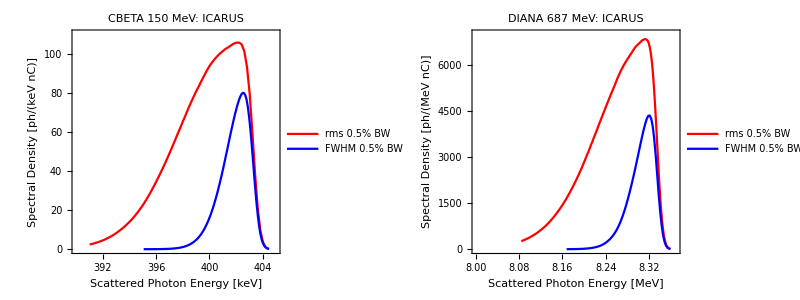

```mathematica
Grid[{{CBETAoptRMSFWHMPLOT,DIANAoptRMSFWHMPLOT}}]
```

## Comparative Tables

The comparative tables all use the head-on cases for ease of comparison with the codes.

## CBETA 150 MeV Table

```mathematica
Grid[{{"CBETA 150 MeV: Collimated Flux Calculations",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Case","My Method","Curatolo et al","3/2γ^2θ_col^2×F","5×F_(0.1  %)","ICARUS","ICCS3D","Units"},{"Baseline",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150base,FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.CBETA150base,"-",CBETAbaseICARUSIntFlux,"-","ph/s"},{"Optimised rms 0.5% BW",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150optRMS,FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS,"-",CBETAoptRMSICARUSIntFlux,CBETAoptRMSICCS3DIntFlux,"ph/s"},{"Optimised FWHM 0.5% BW",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150optFWHM,FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM,5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse]/.CBETA150optFWHM,CBETAoptFWHMICARUSIntFlux,"-","ph/s"}},Dividers->{{True,True,True,True,True,True,True,True,True},{True,True,True,False,False,True}}]
```

CBETA 150 MeV: Collimated Flux Calculations |  |  |  |  |  |  | 
Case | My Method | Curatolo et al | 3/2γ^2θ_col^2×F | 5×F_(0.1  %) | ICARUS | ICCS3D | Units
Baseline | 5.62815×10^9 | 3.72655×10^9 | 5.82924×10^9 | - | 4.93189×10^9 | - | ph/s
Optimised rms 0.5% BW | 3.6009×10^9 | 2.38398×10^9 | 3.69072×10^9 | - | 3.45231×10^9 | 3.57972×10^9 | ph/s
Optimised FWHM 0.5% BW | 1.07534×10^9 | 7.11692×10^8 | 1.07944×10^9 | 9.49271×10^8 | 1.051×10^9 | - | ph/s

```mathematica
Grid[{{"CBETA 150 MeV: Factor Change From My Method (F_ME/F_OTHER)",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Case","Curatolo et al","3/2γ^2θ_col^2×F","5×F_(0.1  %)","ICARUS","ICCS3D"},{"Baseline",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150base),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.CBETA150base),"-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base)/CBETAbaseICARUSIntFlux,"-"},{"Optimised rms 0.5% BW",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150optRMS),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS),"-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS)/CBETAoptRMSICARUSIntFlux,(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS)/CBETAoptRMSICCS3DIntFlux},{"Optimised FWHM 0.5% BW",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM)/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse]/.CBETA150optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM)/CBETAoptFWHMICARUSIntFlux,"-"}},Dividers->{{True,True,True,True,True,True,True},{True,True,True,False,False,True}}]
```

CBETA 150 MeV: Factor Change From My Method (F_ME/F_OTHER) |  |  |  |  | 
Case | Curatolo et al | 3/2γ^2θ_col^2×F | 5×F_(0.1  %) | ICARUS | ICCS3D
Baseline | 1.51028 | 0.965503 | - | 1.14118 | -
Optimised rms 0.5% BW | 1.51046 | 0.975663 | - | 1.04304 | 1.00592
Optimised FWHM 0.5% BW | 1.51096 | 0.996204 | 1.1328 | 1.02315 | -

Notes on CBETA Tables
• Understandable that ICARUS rms is systematically lower than ICCS3D + My calculation in this case, as the run fails to encapsulate the full energy range of the spectra.
• Possible that ICARUS in the baseline case disagrees with the calculation by ~12% as this isn’t a particularly accurate run of ICARUS - the baseline cases are extremely time consuming.
• Some discrepancies are expected between analytical and codes, since the optimisation has been upgraded in the mean time to include the hourglass effect. 
• The 5×F_(0.1%) calculation is only valid in the FWHM case. Of course there is a systematic underestimate here from linearizing around the Compton edge. 
• ICCS3D runs are only available for the rms optimised cases.
• The calculation by Curatolo et al seems to be systematically incorrect. By a factor of ~1.51, which is ~Sqrt[2×Sqrt[2×ln(2)]] = 1.53 ??

## DIANA 687 MeV Table

```mathematica
Grid[{{"DIANA 687 MeV: Collimated Flux Calculations",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Case","My Method","Curatolo et al","3/2γ^2θ_col^2×F","5×F_(0.1  %)","ICARUS","ICCS3D","Units"},{"Baseline",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687base,FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.DIANA687base,"-",DIANAbaseICARUSIntFlux,"-","ph/s"},{"Optimised rms 0.5% BW",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687optRMS,FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS,"-",DIANAoptRMSICARUSIntFlux,DIANAoptRMSICCS3DIntFlux,"ph/s"},{"Optimised FWHM 0.5% BW",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687optFWHM,FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM,5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse]/.DIANA687optFWHM,DIANAoptFWHMICARUSIntFlux,"-","ph/s"}},Dividers->{{True,True,True,True,True,True,True,True,True},{True,True,True,False,False,True}}]
```

DIANA 687 MeV: Collimated Flux Calculations |  |  |  |  |  |  | 
Case | My Method | Curatolo et al | 3/2γ^2θ_col^2×F | 5×F_(0.1  %) | ICARUS | ICCS3D | Units
Baseline | 1.29744×10^10 | 8.74197×10^9 | 1.35746×10^10 | - | 1.2219×10^10 | - | ph/s
Optimised rms 0.5% BW | 9.05462×10^9 | 6.10023×10^9 | 9.42153×10^9 | - | 8.75747×10^9 | 9.08257×10^9 | ph/s
Optimised FWHM 0.5% BW | 2.30186×10^9 | 1.5501×10^9 | 2.34977×10^9 | 2.14561×10^9 | 2.26909×10^9 | - | ph/s

```mathematica
Grid[{{"DIANA 687 MeV: Factor Change From My Method (F_ME/F_OTHER)",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Case","Curatolo et al","3/2γ^2θ_col^2×F","5×F_(0.1  %)","ICARUS","ICCS3D"},{"Baseline",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687base),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.DIANA687base),"-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base)/DIANAbaseICARUSIntFlux,"-"},{"Optimised rms 0.5% BW",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687optRMS),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS),"-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS)/DIANAoptRMSICARUSIntFlux,(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS)/DIANAoptRMSICCS3DIntFlux},{"Optimised FWHM 0.5% BW",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM)/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse]/.DIANA687optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM)/DIANAoptFWHMICARUSIntFlux,"-"}},Dividers->{{True,True,True,True,True,True,True},{True,True,True,False,False,True}}]
```

DIANA 687 MeV: Factor Change From My Method (F_ME/F_OTHER) |  |  |  |  | 
Case | Curatolo et al | 3/2γ^2θ_col^2×F | 5×F_(0.1  %) | ICARUS | ICCS3D
Baseline | 1.48415 | 0.955784 | - | 1.06182 | -
Optimised rms 0.5% BW | 1.48431 | 0.961056 | - | 1.03393 | 0.996923
Optimised FWHM 0.5% BW | 1.48498 | 0.979611 | 1.07282 | 1.01444 | -

Notes on DIANA Tables
• Understandable that ICARUS rms is systematically lower than ICCS3D + My calculation in this case, as the run fails to encapsulate the full energy range of the spectra.
• Possible that ICARUS in the baseline case disagrees with the calculation by ~6% as this isn’t a particularly accurate run of ICARUS - the baseline cases are extremely time consuming.
• Some very small discrepancies are expected between analytical and codes, since the optimisation has been upgraded in the mean time to include the hourglass effect. 
• The 3/2 γ^2 θ_col^2×F calculation is more accurate in the DIANA 687 MeV case as this relies on the small angle approximation and the DIANA collimation angles are smaller.  
• The 5×F_(0.1%) calculation is only valid in the FWHM case. Of course there is a systematic underestimate here from linearizing around the Compton edge. 
• ICCS3D runs are only available for the rms optimised cases.
• The calculation by Curatolo et al seems to be systematically incorrect. By a factor of ~1.48, which is ~Sqrt[2×Sqrt[2×ln(2)]] = 1.53 ?? Lower systematic error may suggest that the Curatolo calculation fails to take into account recoil as well too?

## DIANA + CBETA Combined Differences

```mathematica
Grid[{{"","DIANA 687 MeV: Factor Change From My Method (F_ME/F_OTHER)",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,"CBETA 150 MeV: Factor Change From My Method (F_ME/F_OTHER)",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Case","Curatolo et al","3/2γ^2θ_col^2×F","5×F_(0.1  %)","ICARUS","ICCS3D","Curatolo et al","3/2γ^2θ_col^2×F","5×F_(0.1  %)","ICARUS","ICCS3D"},{"Baseline",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687base),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.DIANA687base),"-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base)/DIANAbaseICARUSIntFlux,"-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150base),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.CBETA150base),"-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base)/CBETAbaseICARUSIntFlux,"-"},{"Optimised rms 0.5% BW",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687optRMS),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS),"-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS)/DIANAoptRMSICARUSIntFlux,(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optRMS)/DIANAoptRMSICCS3DIntFlux,(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150optRMS),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS),"-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS)/CBETAoptRMSICARUSIntFlux,(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optRMS)/CBETAoptRMSICCS3DIntFlux},{"Optimised FWHM 0.5% BW",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM)/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse]/.DIANA687optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687optFWHM)/DIANAoptFWHMICARUSIntFlux,"-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM)/(FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM)/(FAS[Ee,θcol,λ,βIP,ϵn,σL,0,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM)/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse]/.CBETA150optFWHM),(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150optFWHM)/CBETAoptFWHMICARUSIntFlux,"-"}},Dividers->{{True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,False,False,True}}]
```

| DIANA 687 MeV: Factor Change From My Method (F_ME/F_OTHER) |  |  |  |  | CBETA 150 MeV: Factor Change From My Method (F_ME/F_OTHER) |  |  |  | 
Case | Curatolo et al | 3/2γ^2θ_col^2×F | 5×F_(0.1  %) | ICARUS | ICCS3D | Curatolo et al | 3/2γ^2θ_col^2×F | 5×F_(0.1  %) | ICARUS | ICCS3D
Baseline | 1.48415 | 0.955784 | - | 1.06182 | - | 1.51028 | 0.965503 | - | 1.14118 | -
Optimised rms 0.5% BW | 1.48431 | 0.961056 | - | 1.03393 | 0.996923 | 1.51046 | 0.975663 | - | 1.04304 | 1.00592
Optimised FWHM 0.5% BW | 1.48498 | 0.979611 | 1.07282 | 1.01444 | - | 1.51096 | 0.996204 | 1.1328 | 1.02315 | -

## Comparison of Tuning Curves

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/CBETA"];
CBETA150rmsDAT=<<"CBETA150optRMS.txt";
CBETA150fwhmDAT=<<"CBETA150optFWHM.txt";
```

```mathematica
CBETA150RMSFBW=ListLinePlot[Partition[Riffle[CBETA150rmsDAT⟦All,1⟧,CBETA150rmsDAT⟦All,4⟧],2],Frame->True,PlotLabel->"0.5% rms BW Optimisation",FrameLabel->{"rms Bandwidth (%)","Collimated Flux (ph/s)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},ImageSize->Medium];
CBETA150RMSβθ=ListLinePlot[Partition[Riffle[CBETA150rmsDAT⟦All,2⟧,CBETA150rmsDAT⟦All,3⟧],2],Frame->True,PlotLabel->"0.5% rms BW Optimisation",FrameLabel->{"Collimation Angle (mrad)","β function at the IP (m)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotRange->All,ImageSize->Medium];
```

```mathematica
CBETA150RMSFWHMFBW=ListLinePlot[{Partition[Riffle[CBETA150rmsDAT⟦All,1⟧,CBETA150rmsDAT⟦All,4⟧],2],Partition[Riffle[CBETA150fwhmDAT⟦All,1⟧,CBETA150fwhmDAT⟦All,4⟧],2]},PlotStyle->{Red,Blue},Frame->True,PlotLabel->"0.5% BW Optimisations",FrameLabel->{"Bandwidth (%)","Collimated Flux (ph/s)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{"rms 0.5% BW","FWHM 0.5% BW"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],ImageSize->Medium];
```

```mathematica
CBETA150RMSFWHMβθ=ListLinePlot[{Partition[Riffle[CBETA150rmsDAT⟦All,2⟧,CBETA150rmsDAT⟦All,3⟧],2],Partition[Riffle[CBETA150fwhmDAT⟦All,2⟧,CBETA150fwhmDAT⟦All,3⟧],2]},PlotStyle->{Red,Blue},Frame->True,PlotLabel->"0.5% BW Optimisations",FrameLabel->{"Collimation Angle (mrad)","β function at the IP (m)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotRange->{{0.03,0.5},{0,4.3}},PlotLegends->Placed[LineLegend[{"rms 0.5% BW","FWHM 0.5% BW"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.7,0.8}],ImageSize->Medium];
```

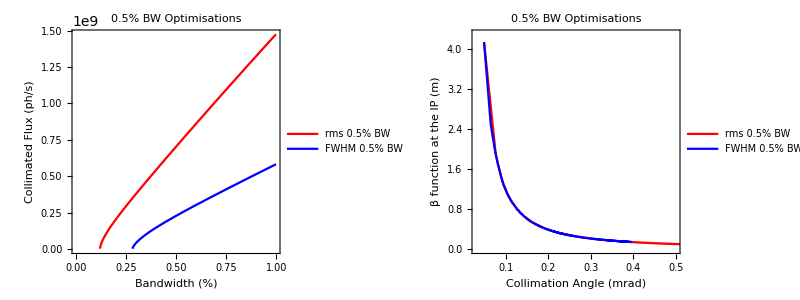

```mathematica
Grid[{{CBETA150RMSFWHMFBW,CBETA150RMSFWHMβθ}}]
```